# NG^4 T_01. Многослойный персептрон

2 курс, 5 группа
Шклярик В.С.
09-фев-2023

### Задание 1. Искусственная нейросеть и логические операции.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
```

```mathematica
kmANN21[{1,2,3}]@{22,-11}
```

1

```mathematica
Clear[kmANN221];
kmANN221[{{W11_,W12_}?MatrixQ, W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{UnitStep[W11.{x1,x2,1}],UnitStep[W12.{x1,x2,1}],1}];
```

```mathematica
kmANN221[{{{1,2,3},{3,2,1}}, {3,3,0}}]@{22,-11}
```

1

```mathematica
{{1,2,3},{3,2,1}}.{22,-11,1}
```

{3,45}

```mathematica
{3,3,0}.Append[{3,45},1]
```

144

```mathematica
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{x1,UnitStep[W1.{x1,x2,1}],x2,1}];
```

```mathematica
kmANN211[{{1,2,3},{4,3,2,0.5}}]@{22,-11}
```

1

```mathematica
ClearAll[kmANN21, kmANN221, kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN221[{{W11_,W12_}?MatrixQ, W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{UnitStep[W11.{x1,x2,1}],UnitStep[W12.{x1,x2,1}],1}];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{x1,UnitStep[W1.{x1,x2,1}],x2,1}];
```

```mathematica
And@@#&/@BooleDS
```

BooleDS

```mathematica
{0&&0,0&&1,1&&0,1&&1}/.{0->False,1->True}/.{False->0,True->1}
```

{0,0,0,1}

```mathematica
Apply[And,{0,1}]
```

0&&1

```mathematica
BooleDS=Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
Do[Print[op,":",MapThread[StringJoin[ToString@#1," → ",ToString@#2]&,{BooleDS,op@@#&/@BooleDS/.{0->False,1->True}/.{False->0,True->1} }]],{op,{And,Or,Xor}}];
```

{{0,0},{0,1},{1,0},{1,1}}

And:{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

Or:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 1}

Xor:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 0}

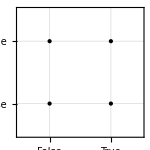

```mathematica
Fig1 = Graphics[{PointSize@Medium, Point@BooleDS}, ImageSize->150, Frame->True,FrameStyle->Thick, FrameTicks->{#,#}&@{{{0,Style[False,Red]},{1,Style[True,Blue]}},None},PlotRange->{{-.5,1.5},{-.5,1.5}},GridLines->{{0,1},{0,1}} ]
```

Выберем подходящие веса w_1,w_2,w_0 для корректной работы нашей реализации оператора And. Зная, как работает функция UnitStep и используя подготовленную нами таблицу пар логических констант, сделаем некоторые выводы относительно подходящих значений для вектора весов.
{0,0}→0:		w_0<0
{1,0}→0:		w_1+w_0<0
{1,0}→0:		w_2+w_0<0
{1,1}→1:		w_1+w_2+w_0≥0
В качестве вектора весов можно взять {2,2,-3}.

```mathematica
FindInstance[c<0&&a+c<0&&b+c<0&&a+b+c≥0,{a,b,c},Integers]
```

{{a→3,b→3,c→-6}}

```mathematica
LO=kmAnd=kmANN21[{2,2,-3}];
#->LO@#&/@BooleDS
Show[Fig1, DensityPlot[LO@{x1,x2}, {x1,-.5,1.5},{x2,-.5,1.5}, ColorFunction->(If[#<0.1, Opacity[0,Gray],Opacity[0.3,Gray]]&)],Graphics[{PointSize@Large, {LO@#/.{0->Red,1->Blue}, Point@#}&/@BooleDS}]]
```

{{0,0}→0,{0,1}→0,{1,0}→0,{1,1}→1}

-Graphics-

Рассуждая аналогичным образом придем к выводу, что в качестве вектора весов для нашей реализации оператора Or можно выбрать вектор {2,2,-1}.

```mathematica
LOr=kmOr=kmANN21[{2,2,-1}];
#->LOr@#&/@BooleDS
Show[Fig1, DensityPlot[LOr@{x1,x2}, {x1,-.5,1.5},{x2,-.5,1.5}, ColorFunction->(If[#<0.1, Opacity[0,Gray],Opacity[0.3,Gray]]&)],Graphics[{PointSize@Large, {LOr@#/.{0->Red,1->Blue}, Point@#}&/@BooleDS}]]
```

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→1}

-Graphics-

Для Xor сначала я вычисляла веса так, как показано ниже, и картинка прилагается. Все вроде правильно, только выделяет кривую область.

```mathematica
ClearAll[f,g];
f[x1_,x2_]:={x,y,z}.{UnitStep[{a,b,c}.{x1,x2,1}],UnitStep[{d,e,p}.{x1,x2,1}],1};
```

```mathematica
FindInstance[f[0,0]<0&&f[1,0]≥0&&f[0,1]≥0&&f[1,1]<0,{a,b,c,d,e,p,x,y,z},Integers]
```

{{a→-4,b→-4,c→4,d→-3,e→-3,p→0,x→2,y→-4,z→-2}}

```mathematica
{{{-4,-4,4},{-3,-3,0}},{2,-4,-2}};
```

```mathematica
LXOR1=kmXor=kmANN221[{{{-4,-4,4},{-3,-3,0}},{2,-4,-2}}];
#->LXOR1@#&/@BooleDS
Show[Fig1, DensityPlot[LXOR1@{x1,x2}, {x1,-.5,1.5},{x2,-.5,1.5}, ColorFunction->(If[#<0.1, Opacity[0,Gray],Opacity[0.3,Gray]]&)],Graphics[{PointSize@Large, {LXOR1@#/.{0->Red,1->Blue}, Point@#}&/@BooleDS}]]
```

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→0}

-Graphics-

Потом уже поняла что для “ровной” области надо взять “не И” и “ИЛИ” (т.е. их вектора весов) для первого слоя, и “И” для второго(как их пересечение).

```mathematica
LXOR1=kmXor=kmANN221[{{{2,2,-1},{-2,-2,3}},{2,2,-3}}];
#->LXOR1@#&/@BooleDS
Show[Fig1, DensityPlot[LXOR1@{x1,x2}, {x1,-.5,1.5},{x2,-.5,1.5}, ColorFunction->(If[#<0.1, Opacity[0,Gray],Opacity[0.3,Gray]]&)],Graphics[{PointSize@Large, {LXOR1@#/.{0->Red,1->Blue}, Point@#}&/@BooleDS}]]
```

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→0}

-Graphics-

Тут сначала снова тем же методом решала уравнение, получилась интересная область (чтоб ее как-то отобразить поменяла местами выражения в if).

```mathematica
g[x1_,x2_]:={d,e,p,h}.{x1,UnitStep[{a,b,c}.{x1,x2,1}],x2,1};
FindInstance[g[0,0]<0&&g[1,0]≥0&&g[0,1]≥0&&g[1,1]<0,{a,b,c,d,e,p,h},Integers]
```

{{a→-4,b→-4,c→4,d→3,e→7,p→3,h→-10}}

```mathematica
LXOR2=kmXor2=kmANN211[{{-4,-4,4},{3,7,3,-10}}];
#->LXOR2@#&/@BooleDS
Show[Fig1, DensityPlot[LXOR2@{x1,x2}, {x1,-.5,1.5},{x2,-.5,1.5}, ColorFunction->(If[#<0.2, Opacity[0.3,Gray],Opacity[0,Gray]]&)],Graphics[{PointSize@Large, {LXOR2@#/.{0->Red,1->Blue}, Point@#}&/@BooleDS}]]
```

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→0}

-Graphics-

Новая попытка получить другую картинку:
Сначала входные числа проверяем на “И” - должны получить 0 (веса на “И” мы знаем: {2,2,-3}), а потом на “ИЛИ” - должны получить 1 (веса тоже знаем: {2,2,-1}). Найти нужно только вес, с которым первый нейрон передает 1 или 0 второму.
На бумажке рассмотрела возможные пары входных чисел, и помогает отыскать нужный вес пара {1,1}: первая проверка на “И” выдаст 1, и последний нейрон будет выдавать UnitStep[1*2+1*w+1*2-1] = UnitStep[3+w], что должно равняться 0, т.е. искомый вес должен быть меньше, чем -3. Выберем -4 и получим картинку, симметричную предложенной в тексте лабораторной.

```mathematica
LXOR2=kmXor2=kmANN211[{{2,2,-3},{2,-4,2,-1}}];
#->LXOR2@#&/@BooleDS
Show[Fig1, DensityPlot[LXOR2@{x1,x2}, {x1,-.5,1.5},{x2,-.5,1.5}, ColorFunction->(If[#<0.1, Opacity[0,Gray],Opacity[0.3,Gray]]&)],Graphics[{PointSize@Large, {LXOR2@#/.{0->Red,1->Blue}, Point@#}&/@BooleDS}]]
```

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→0}

-Graphics-

### Задание 2. Покрытие области полуплоскостями.

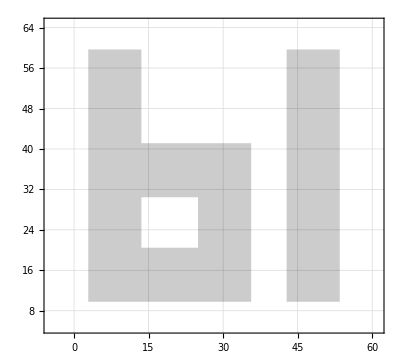
{Ы,-Graphics-,{{2.8512,9.77672},{2.8512,59.6727},{13.5432,59.6727},{13.5432,41.1399},{35.64,41.1399},{35.64,9.77672},{13.5432,30.4479},{13.5432,20.4687},{24.948,20.4687},{24.948,30.4479},{42.768,59.6727},{53.46,59.6727},{53.46,9.77672},{42.768,9.77672}}}

```mathematica
{Letter, FigLetter, Vertices} = Apply[{First@#1, Uncompress@Last@#1,{##2}}&, Import["NG23T01Problem.xlsx",{"Sheets","Шклярик Вера" }]]
```

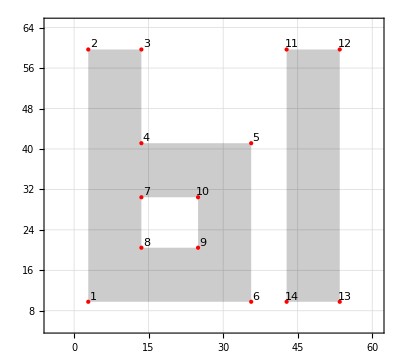

```mathematica
Show[FigLetter, Graphics[{PointSize[Large], Red,Point@Vertices}], Graphics[MapIndexed[Text[First@#2,#1]&,Vertices+1]]]
```

```mathematica
ClearAll[kmHalfPlane];
kmHalfPlane[{P1_,P2_}]:=HalfPlane[{P1,P2},{(P1-P2)⟦2⟧,-(P1-P2)⟦1⟧}]
```

```mathematica
L1 = {{2,1},{13,12},{12,2},{1,13},{11,14},{4,3},{9,8},{5,4},{7,10},{6,5},{10,9}};
```

```mathematica
Manipulate[Labeled[Show[FigLetter, Graphics[{PointSize[Large], Red,Point@Vertices}], Graphics[MapIndexed[Text[First@#2,#1]&,Vertices+1]],Graphics[{Opacity[0.1,Purple],kmHalfPlane[Vertices⟦n⟧]}]],Dynamic@Style[StringForm["Точки: `` ⟶ ``", Sequence@@n]],Top],{{n, First[L1],"Полуплоскость"},MapIndexed[#1->ToString[First[#2]]&,L1]}, ControlType->SetterBar, ControlPlacement->Top]
```

### Задание 3. Искусственный нейрон.

```mathematica
ClearAll[kmANN];
kmANN[W_?VectorQ]:=Sign[W.Append[#,1]]&;
```

```mathematica
kmANN[{3,2,1}]@{3,3}
```

1

```mathematica
kmANN[{{3,2,1,3},{0,3,4,0.5}}]@{3,-4,-8}
```

kmANN[{{3,2,1,3},{0,3,4,0.5}}][{3,-4,-8}]

Краткий комментарий по поводу функции  getWeight: 
A (x - x0) + B (y - y0) = 0
n(A,B)
M0(x0,y0).

```mathematica
ClearAll[getWeight,A,B];
getWeight[{P1_,P2_}]:=With[{A=Normalize[{(P1-P2)⟦2⟧,-(P1-P2)⟦1⟧}]⟦1⟧, B = Normalize[{(P1-P2)⟦2⟧,-(P1-P2)⟦1⟧}]⟦2⟧}, {A,B, -A*P1⟦1⟧-B*P1⟦2⟧}]
```

```mathematica
getWeight[{{3,3},{9,0}}]
```

{1/(√5),2/(√5),-9/(√5)}

```mathematica
weights1 = getWeight/@(Vertices⟦#⟧&/@L1)
```

{{1.,0.,-2.8512},{-1.,0.,53.46},{0.,-1.,59.6727},{0.,1.,-9.77672},{1.,0.,-42.768},{-1.,0.,13.5432},{0.,-1.,20.4687},{0.,-1.,41.1399},{0.,1.,-30.4479},{-1.,0.,35.64},{1.,0.,-24.948}}

```mathematica
Export1=Prepend[MapThread[Join,{L1,weights1}],{"From", "To", "W1", "W2", "W0"}]
```

{{From,To,W1,W2,W0},{2,1,1.,0.,-2.8512},{13,12,-1.,0.,53.46},{12,2,0.,-1.,59.6727},{1,13,0.,1.,-9.77672},{11,14,1.,0.,-42.768},{4,3,-1.,0.,13.5432},{9,8,0.,-1.,20.4687},{5,4,0.,-1.,41.1399},{7,10,0.,1.,-30.4479},{6,5,-1.,0.,35.64},{10,9,1.,0.,-24.948}}

```mathematica
Export["NG4T01 ШклярикВера.xlsx", "Layer1"->Export1, "FormattedData"]
```

NG4T01 ШклярикВера.xlsx

```mathematica
Manipulate[Labeled[Show[FigLetter, Graphics[{PointSize[Large], Red,Point@Vertices}], Graphics[MapIndexed[Text[First@#2,#1]&,Vertices+1]],Graphics[DensityPlot[kmANN[weights1[[Нейрон]]]@{x1,x2}, {x1,-5,65},{x2,5,65},ColorFunctionScaling->False,ColorFunction->(Piecewise[{{Opacity[.2,Purple], 0<#}, {Opacity[0,Purple], True}}]&)]]],Style[ToString[Subscript[W,1, Нейрон], TraditionalForm]<>ToString@StringForm[" = ``",ToString[ weights1⟦Нейрон⟧]],Purple, Bold],Top],{Нейрон, Range[Length@L1]}, ControlType->SetterBar, ControlPlacement->Top]
```

### Задание 4. Однослойный персептрон.

```mathematica
ClearAll[kmANN];
kmANN[W_?VectorQ]:=Sign[W.Append[#,1]]&;
kmANN[W_?MatrixQ]:=Sign[#]&/@W.Append[#,1]&;
```

```mathematica
lst = {};
If[#<0,Append[lst,{{2,1}->Red}]]&;
Flatten[MapIndexed[If[#1<0,Append[lst,{2,First@#2}->Red],Append[lst,{2,First@#2}->Blue]]&,kmANN[weights1]@{30,30} ],1]
```

{{2,1}→RGBColor[0, 0, 1],{2,2}→RGBColor[1, 0, 0],{2,3}→RGBColor[1, 0, 0],{2,4}→RGBColor[0, 0, 1],{2,5}→RGBColor[0, 0, 1],{2,6}→RGBColor[1, 0, 0],{2,7}→RGBColor[1, 0, 0],{2,8}→RGBColor[1, 0, 0],{2,9}→RGBColor[0, 0, 1],{2,10}→RGBColor[1, 0, 0],{2,11}→RGBColor[0, 0, 1]}

```mathematica
lst = {};
P={30,30};
Dynamic[P];
Manipulate[Labeled[LocatorPane[Dynamic@P, Show[FigLetter,Graphics[{PointSize[Large], Red,Point@Vertices}],Graphics[MapIndexed[Text[First@#2,#1]&,Vertices+1]],Graphics[DensityPlot[kmANN[weights1[[Нейрон]]]@{x1,x2}, {x1,-5,65},{x2,5,65},ColorFunctionScaling->False,ColorFunction->(Piecewise[{{Opacity[.2,Purple], 0<#}, {Opacity[0,Purple], True}}]&) ]]]],Dynamic@Grid[{Range@Length@weights1,kmANN[weights1]@P}, Frame->All,Background->{{Нейрон->Pink},None},
ItemStyle->{Automatic,Automatic,Flatten[MapIndexed[If[#1<0,Append[lst,{2,First@#2}->{Red,Bold,14}],Append[lst,{2,First@#2}->{Blue, Bold,14}]]&,kmANN[weights1]@P ],1]}], Top], {Нейрон, Range[11]}, ControlType->SetterBar, ControlPlacement->Top]
```

### Задание 5. Выпуклый многоугольник.

```mathematica
Graphics[ kmHalfPlane@Vertices⟦{13,12}⟧];
```

```mathematica
HP = kmHalfPlane@Vertices⟦#⟧&/@L1;
```

```mathematica
L2 = {#2∧#3∧#4∧#5&,#1∧#3∧#4∧#10&,¬#5∧¬#6∧¬#8&,¬#6∧¬#7∧¬#9∧¬#11&}
```

{#2&&#3&&#4&&#5&,#1&&#3&&#4&&#10&,!#5&&!#6&&!#8&,!#6&&!#7&&!#9&&!#11&}

```mathematica
BooleanRegion[#,HP]&/@L2;
```

```mathematica
Manipulate[Show[FigLetter,Region[Style[BooleanRegion[n,HP], Opacity[.3,Purple]]]],{ {n,First@L2, "Выпуклый четырехугольник"}, Thread[L2->Range@Length@L2], SetterBar,ControlPlacement->Top}]
```

### Задание 6. Двухслойный персептрон.

```mathematica
ClearAll[kmANN];
kmANN[W_?VectorQ]:=Sign[W.Append[#,1]]&;
kmANN[W_?MatrixQ]:=Sign[W.Append[#,1]]&;
kmANN[W:{__?MatrixQ}]:=Function[x,Fold[kmANN[#2]@#1&,x,W]];
```

```mathematica
L2
```

{#2&&#3&&#4&&#5&,#1&&#3&&#4&&#10&,!#5&&!#6&&!#8&,!#6&&!#7&&!#9&&!#11&}

```mathematica
weights2 = {{0,1,1,1,1,0,0,0,0,0,0,-3.5},{1,0,1,1,0,0,0,0,0,1,0,-3.5},{0,0,0,0,-1,-1,0,-1,0,0,0,-2.5},{0,0,0,0,0,-1,-1,0,-1,0,-1,-3.5}};
```

```mathematica
ClearAll[ANN,ANN2];
ANN = kmANN@{weights1,weights2};
```

```mathematica
{ANN@{30,30}, ANN@{20,25}}
```

{{-1,1,-1,-1},{-1,1,-1,1}}

```mathematica
Flatten[{"Polygon", Table[StringJoin["W", ToString@i],{i,1,11}]
,"W0"}];
Export2=Prepend[MapThread[Prepend,{weights2, L2}], Flatten[{"Polygon", Table[StringJoin["W", ToString@i],{i,1,11}]
,"W0"}]]
```

{{Polygon,W1,W2,W3,W4,W5,W6,W7,W8,W9,W10,W11,W0},{#2&&#3&&#4&&#5&,0,1,1,1,1,0,0,0,0,0,0,-3.5},{#1&&#3&&#4&&#10&,1,0,1,1,0,0,0,0,0,1,0,-3.5},{!#5&&!#6&&!#8&,0,0,0,0,-1,-1,0,-1,0,0,0,-2.5},{!#6&&!#7&&!#9&&!#11&,0,0,0,0,0,-1,-1,0,-1,0,-1,-3.5}}

```mathematica
Export["NG4T01 ШклярикВера.xlsx", {"Layer1"->Export1,"Layer2"->Export2}, "FormattedData"]
```

NG4T01 ШклярикВера.xlsx

```mathematica
ANN@P
```

{-1,1,-1,-1}

```mathematica
lst = {};
P={30,30};
Dynamic[P];
Manipulate[Labeled[LocatorPane[Dynamic@P, Show[FigLetter,Region[Style[BooleanRegion[Четырехугольник,HP], Opacity[.3,Purple]]]]],Dynamic@Grid[{Range@Length@L2,ANN@P}, Frame->All,Background->{{First@Flatten@Position[L2,Четырехугольник ]->Pink},None},
ItemStyle->{Automatic,Automatic,Flatten[MapIndexed[If[#1<0,Append[lst,{2,First@#2}->{Red,Bold,14}],Append[lst,{2,First@#2}->{Blue, Bold,14}]]&,ANN@P ],1]}], Top],{ {Четырехугольник,First@L2}, Thread[L2->Range@Length@L2], SetterBar,ControlPlacement->Top}]
```

### Задание 7. Трехслойный персептрон.

```mathematica
L3 = (#1∨#2)∧¬#3∧¬#4&
```

(#1||#2)&&!#3&&!#4&

```mathematica
weights3 = {{1,1,-1,-1,-.5}}
```

{{1,1,-1,-1,-0.5}}

Будет достаточно взять вес-смещение -0.5, т.к., если первые два вернут по -1, сумма будет равна 0, значит достаточно взять любое отрицательное число в качестве смещения.

```mathematica
Prepend[First@weights3,ToString@L3]
```

{(#1 || #2) && !#3 && !#4 & ,1,1,-1,-1,-0.5}

```mathematica
Flatten[{"Polygon", Table[StringJoin["W", ToString@i],{i,1,4}]
,"W0"}];
Export3=Prepend[{Prepend[First@weights3,ToString@L3]}, Flatten[{"Polygon", Table[StringJoin["W", ToString@i],{i,1,4}]
,"W0"}]]
```

{{Polygon,W1,W2,W3,W4,W0},{(#1 || #2) && !#3 && !#4 & ,1,1,-1,-1,-0.5}}

```mathematica
Export["NG4T01 ШклярикВера.xlsx", {"Layer1"->Export1,"Layer2"->Export2,"Layer3"->Export3}, "FormattedData"]
```

NG4T01 ШклярикВера.xlsx

```mathematica
ANN2 = kmANN@{weights1,weights2, weights3};
{ANN2@{30,30}, ANN2@{20,25}}
```

{{1},{-1}}

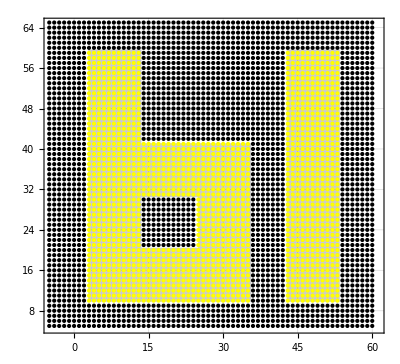
-Graphics-Обучающий набор

```mathematica
Labeled[Show[FigLetter,Graphics[{Table[{If[First@ANN2@{x,y}<1,Black , Yellow], Point@{x,y}},{x,-5,60},{y,5,65}]}]],Text@Style["Обучающий набор", Black, Large, Bold], Top]
```

```mathematica
P={30,30};
Dynamic[P];
Labeled[LocatorPane[Dynamic@P,FigLetter,Appearance->Graphics[{PointSize[Large],Dynamic[RGBColor[#]&@If[First@ANN2@P<1,{1,0,0}, {0,0,1}]], Point@P}]],Dynamic@Text[Style[StringForm["`` ",Dynamic@P],If[First@ANN2@P<1,Red, Blue], Large, Bold]], Top]
```

```mathematica
RGBColor[#]&@If[First@ANN2@P<1,{1,0,0}, {0,0,1}]
```

RGBColor[{0, 0, 1}]

```mathematica
If[First@ANN2@P<1,{1,0,0}, {0,0,1}]
```

{0,0,1}